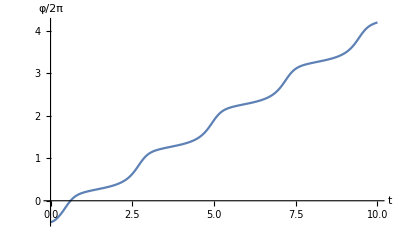

```mathematica
tmax=10;
Ta=10;
wd=0.4;(*Отвечает за диссипативные процессы, чем меньше wd, тем меньше затухание*)
wp=0.6;
a=1.3;
b=wd/(wp^2 Ta);
solution=NDSolve[{x'[t]==y[t],1/Ta^2 y'[t]==a*wp^2-wp^2*Sin[x[t]]-b*y[t],x[0]==-Pi,y[0]==0},{x,y},{t,20}];
ParametricPlot[{Evaluate[Mod[x[t],2Pi]]/.solution,Evaluate[y[t]]/.solution},{t,0,tmax},PlotRange->All];
ParametricPlot[Evaluate[{x[t],y[t]}/.solution],{t,0,tmax}(*,PlotRange->All*)];
Plot[Evaluate[y[t]/.solution],{t,0,tmax},PlotRange->All];
Plot[Evaluate[x[t]/.solution]/(2Pi),{t,0,tmax},PlotRange->All,AxesLabel->{"t","φ/2π"}]
```

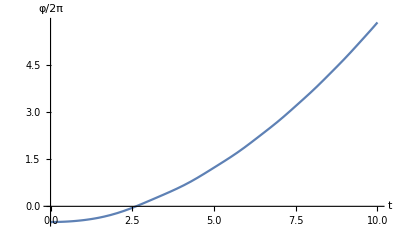

```mathematica
tmax=10;
wp=0.8;
a=1.1;
solution=NDSolve[{x'[t]==y[t],y'[t]==a*wp^2-(*x[t]*)wp^2*Sin[x[t]],x[0]==-Pi,y[0]==0},{x,y},{t,20}];
ParametricPlot[Evaluate[{x[t],y[t]}/.solution],{t,0,tmax}(*,PlotRange->All*)];
Plot[Evaluate[x[t]/.solution]/(2Pi),{t,0,tmax}(*,PlotRange->All*),AxesLabel->{"t","φ/2π"}]
```

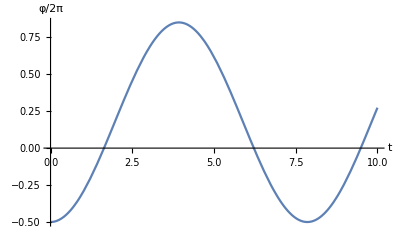

```mathematica
tmax=10;
wp=0.8;
a=1.1;
solution=NDSolve[{x'[t]==y[t],y'[t]==a*wp^2-x[t] wp^2,x[0]==-Pi,y[0]==0},{x,y},{t,20}];
ParametricPlot[Evaluate[{x[t],y[t]}/.solution],{t,0,tmax}(*,PlotRange->All*)];
Plot[Evaluate[x[t]/.solution]/(2Pi),{t,0,tmax}(*,PlotRange->All*),AxesLabel->{"t","φ/2π"}]
```